```mathematica
eq1:= (sig^2-k^2*va^2)*dvx + 2*I*sig*omega*dvy+sig*kx*W;
eq2:=(sig^2-kz^2*va^2)*dvy - I(shear*va^2*kz^2/sig+sig*kappa^2/(2*omega))*dvx;
eq3:=(sig^2/csq-kz^2)*W + sig*kx*dvx;
Solve[{eq1==-sig*kx*dphi,eq2==0,eq3==kz^2*dphi},{dvx,dvy,W}]
```

{{dvx→-((-dphi kx kz^2 sig-dphi kx sig (-kz^2+sig^2/csq)) (sig^2-kz^2 va^2))/(2 omega sig (-kz^2+sig^2/csq) ((kappa^2 sig)/(2 omega)+(kz^2 shear va^2)/sig)+(sig^2-kz^2 va^2) (kx^2 sig^2-(-kz^2+sig^2/csq) (sig^2-k^2 va^2))),dvy→-(ⅈ (-dphi kx kz^2 sig-dphi kx sig (-kz^2+sig^2/csq)) ((kappa^2 sig)/(2 omega)+(kz^2 shear va^2)/sig))/(2 omega sig (-kz^2+sig^2/csq) ((kappa^2 sig)/(2 omega)+(kz^2 shear va^2)/sig)+(sig^2-kz^2 va^2) (kx^2 sig^2-(-kz^2+sig^2/csq) (sig^2-k^2 va^2))),W→-dphi+((-dphi kx kz^2 sig-dphi kx sig (-kz^2+sig^2/csq)) (sig^2-kz^2 va^2) ((sig^2-k^2 va^2)/(kx sig)-(2 omega ((kappa^2 sig)/(2 omega)+(kz^2 shear va^2)/sig))/(kx (sig^2-kz^2 va^2))))/(2 omega sig (-kz^2+sig^2/csq) ((kappa^2 sig)/(2 omega)+(kz^2 shear va^2)/sig)+(sig^2-kz^2 va^2) (kx^2 sig^2-(-kz^2+sig^2/csq) (sig^2-k^2 va^2)))}}

```mathematica
FullSimplify[((-dphi kx kz^2 sig-dphi kx sig (-kz^2+sig^2/csq)) (sig^2-kz^2 va^2) ((sig^2-k^2 va^2)/(kx sig)-(2 omega ((kappa^2 sig)/(2 omega)+(kz^2 shear va^2)/sig))/(kx (sig^2-kz^2 va^2))))/(2 omega sig (-kz^2+sig^2/csq) ((kappa^2 sig)/(2 omega)+(kz^2 shear va^2)/sig)+(sig^2-kz^2 va^2) (kx^2 sig^2-(-kz^2+sig^2/csq) (sig^2-k^2 va^2)))]
```

(dphi sig^2 (-kappa^2 sig^2-2 kz^2 omega shear va^2+(sig-k va) (sig+k va) (sig-kz va) (sig+kz va)))/(csq kappa^2 kz^2 sig^2-(kappa^2+csq (kx^2+kz^2)) sig^4+sig^6+(2 csq kz^4 omega shear+kz^2 (csq (k^2+kx^2+kz^2)-2 omega shear) sig^2-(k^2+kz^2) sig^4) va^2+k^2 kz^2 (-csq kz^2+sig^2) va^4)

```mathematica
wtilde=w+pot;
ksq=kx^2+kz^2;
momx:=vasq*ksq*vx+I*sig(I*sig*vx - 2*om*vy+I*kx*wtilde);
momy:=vasq*kz^2(vy+I*shear*vx/sig)+I*sig(I*sig*vy+kappa2*vx/(2*om));
cont:=-kz^2*wtilde+sig^2*w/csq+sig*kx*vx;
pois:=ksq*pot+om^2*w/(csq*Q);
mat={{vasq*ksq -sig^2,-2I*om*sig,-sig*kx,-sig*kx},
          {I*shear*vasq*kz^2/sig+I*sig*kappa2/(2*om),vasq*kz^2-sig^2,0,0},
{sig*kx,0,sig^2/csq-kz^2,-kz^2},
{0,0,om^2/(csq*Q),ksq} }
detm=FullSimplify[Det[mat]];
```

{{-sig^2+(kx^2+kz^2) vasq,-2 ⅈ om sig,-kx sig,-kx sig},{(ⅈ kappa2 sig)/(2 om)+(ⅈ kz^2 shear vasq)/sig,-sig^2+kz^2 vasq,0,0},{kx sig,0,-kz^2+sig^2/csq,-kz^2},{0,0,om^2/(csq Q),kx^2+kz^2}}

```mathematica
FullSimplify[Collect[detm*csq,sig]]
```

(kx^2+kz^2) sig^6-(kz^4 (om^2-csq (kx^2+kz^2) Q) vasq (2 om shear-(kx^2+kz^2) vasq))/Q-((kx^2+kz^2) sig^4 (-om^2+Q (kappa2+csq (kx^2+kz^2)+(kx^2+2 kz^2) vasq)))/Q+1/Q kz^2 sig^2 (-kappa2 om^2+csq kappa2 (kx^2+kz^2) Q+(kx^2+kz^2) vasq (-2 om^2-2 om Q shear+(kx^2+kz^2) Q (2 csq+vasq)))

```mathematica
y[kx_]=(kx^2+kz^2) sig^6-(kz^4 (om^2-csq (kx^2+kz^2) Q) vasq (2 om shear-(kx^2+kz^2) vasq))/Q-((kx^2+kz^2) sig^4 (-om^2+Q (kappa2+csq (kx^2+kz^2)+(kx^2+2 kz^2) vasq)))/Q+1/Q kz^2 sig^2 (-kappa2 om^2+csq kappa2 (kx^2+kz^2) Q+(kx^2+kz^2) vasq (-2 om^2-2 om Q shear+(kx^2+kz^2) Q (2 csq+vasq)));
```

```mathematica
y[0]
```

kz^2 sig^6-(kz^4 (om^2-csq kz^2 Q) vasq (2 om shear-kz^2 vasq))/Q-(kz^2 sig^4 (-om^2+Q (kappa2+csq kz^2+2 kz^2 vasq)))/Q+(kz^2 sig^2 (-kappa2 om^2+csq kappa2 kz^2 Q+kz^2 vasq (-2 om^2-2 om Q shear+kz^2 Q (2 csq+vasq))))/Q

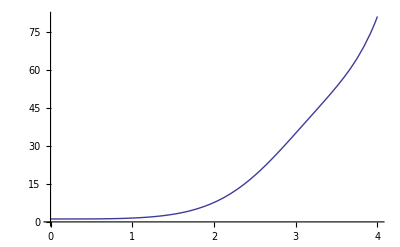

```mathematica
Plot[Abs[MathieuC[-2,-1,z]],{z,0,4}]
```

```mathematica
N[MathieuC[-2,-1,0]]
```

0.450197+1.06234 ⅈ